# 第三次作业

Mathematica 9.0.1 Long Wang

## 第六章

### 2. 设某字典组合 { 016, 087, 154, 170, 275, 426, 503, 509, 512, 612, 653, 677, 703, 765, 897, 908 } 依次顺序表示在内存中，现用二分法的方法检索字典中是否有元素612，问需要进行几次比较才能得出结论？ 每次选择的比较对象是什么元素？

3 次比较： 
    1      2      3      4      5      6      7      8^1     9    10^3   11    12^2  13    14    15    16
{ 016, 087, 154, 170, 275, 426, 503, 509, 512, 612, 653, 677, 703, 765, 897, 908 } 

509, 677, 612.

### 5. 顺序检索时间为O(n), 二分法检索时间为O(log_2 n), 散列法为O(1)，为什么有高效率的检索方法而低效率的方法不被放弃？

不同检索方法有各自的适用条件。

1. 使用不同的存储结构

顺序检索：顺序/链接存储；
二分法检索： 顺序存储且排序；
散列检索：散列存储，依赖散列函数。

2. 算法复杂度

散列/二分法检索，算法实现比顺序检索复杂。对于小数目n的检索，散列/二分法检索的优势难以体现，甚至可能因为实现上的复杂而拖慢了整体的效率。

3. 综合效能

单纯考虑检索时间只能表明检索上的优劣，但实际应用中还需要考虑其他部分的效率，比如二分法检索需要保证排序，在插入与删除中需要很多操作，对于经常需要插入删除的数据，就不是很适用。散列表需要针对不同的数据考虑不同的散列函数，需要合理的解决碰撞，负载因子等问题。

### 算法3. 若线性表中各结点的检索概率不等，则可用如下策略提供顺序检索的效率：若找到指定的结点，则将该结点和其前驱交换，使经常被检索的结点尽量位于表的前端。试对线性表的顺序存储结构和链式存储结构写出实现上述策略的顺序检索算法（必须从表头开始扫描）

顺序表：

template <typename Data> struct ListHeader{
  Data *list;
  int N_MAX;
  int N_STORE;

  //constructor=======================================//
  ListHeader(int n): N_MAX(n), N_STORE(0) {
    list=new Data[n];
    if(!list) {
      fprintf(stderr,"Error: memory allocate fail!\n");
      exit(0);
    }
  }

  //destructor========================================//
  ~ListHeader() {
    if (list) delete list;
    N_STORE=0;
    N_MAX=0;
  }

  //add data==========================================//
  void push_back(Data i){
    if (N_STORE<N_MAX) {
      list[N_STORE]=i;
      N_STORE++;
    }
    else {
      fprintf(stderr,"Error: List Overflow!\n");
      exit(0);
    }
  }

  //search============================================//
  int search(Data i) {
    if (!list) return -1; //Empty List;
    if (list[0]==i) return 0; //First element match;
    else for (int j=1;j<N_STORE;j++) {
        if (list[j]==i) {
          list[j]=list[j-1];
          list[j-1]=i;
          return j-1;
        }
      }
    return -3; //No match
  }
};

链表：

// Data Link List
template <typename Data> struct ListMember{
  Data info;
  ListMember *next;

  //constructor=======================================//
  ListMember(Data i): info(i) {}
  
  //destructor========================================//
  ~ListMember() {
    if (next) delete next;
  }
};

// Data Link Header
template <typename Data> struct ListHeader{
  ListMember<Data> *p;
  ListMember<Data> *last;
  int n;

  //constructor=======================================//  
  ListHeader(): p(0), last(0), n(0) {}

  //destructor========================================//
  ~ListHeader() {
    if (p) delete p;
    last=0;
    n=0;
  }
  
  //Add new member at the end=========================//   
  void push_back(Data i){
    if (!n) {
      p=new ListMember<Data>(i);
      last=p;
      n++;
    }
    else{
      ListMember<Data> *inew=new ListMember<Data>(i);
      if(!inew) {
      	fprintf(stderr,"Error: memory allocate fail!\n");
      	exit(0);
      }
      last->next=inew;
      last=inew;
      n++;
    }
  }
  
  //Search============================================// 
  ListMember<Data>* search(Data i){
    if (!p) return 0; //Empty List;
    if (p->info==i) return p; //If first element match;
    else if(p->next){  //If second is non-zero, continue to search;
      ListMember<Data> *n1=p;
#ifdef EX_INFO    //Method 1: Exchange information only
      ListMember<Data> *n2=p->next;
      while(n2){
        if (n2->info==i) {
          n2->info=n1->info;
          n1->info=i;
          return n1;
        }
        else {
          n1=n1->next;
          n2=n2->next;
        }
      }
#else             //Method 2: Rebuild link;
      if (p->next->info==i) {  //If second match, exchange first two, relink header pointer;
        p=p->next;
        n1->next=p->next;
        p->next=n1;
        return p;
      }
      else if(p->next->next){  //If third is non-zero search till the end
        ListMember<Data> *n2=p->next->next;
        int count=2;
        while(n2){
          if(n2->info==i) {
            ListMember<Data> *tmp=n1->next;
            n1->next=n2;
            tmp->next=n2->next;
            n2->next=tmp;
            return n1->next;
          }
          else {
            n1=n1->next;
            n2=n2->next;
          }
        }
      }
#endif        
    }
    return 0; //No match;
  }
};

## 第七章

### 2. 设有关键码 a, b, c, d, 按照不同的输入顺序，共可能组成多少不同的二叉排序树。请画出其中高度较小的六种。

#### #code

```mathematica
Gplot[g_,s_]:=GraphPlot[g[[1]],
VertexLabeling->True,VertexCoordinateRules->g[[2]],ImageSize->s]
g=
{{{a->b,b->c,c->d},{a->{-1,2},b->{0,1},c->{1,0},d->{2,-1}}},
{{a->b,b->d,d->c},{a->{-1,2},b->{0,1},d->{2,0},c->{1,-1}}},
{{a->d,d->b,b->c},{a->{-1,2},d->{2,1},b->{0,0},c->{1,-1}}},
{{a->d,d->c,c->b},{a->{-1,2},d->{2,1},c->{1,0},b->{0,-1}}},
{{d->c,c->b,b->a},{d->{2,2},c->{1,1},b->{0,0},a->{-1,-1}}},
{{d->c,c->a,a->b},{d->{2,2},c->{1,1},a->{-1,0},b->{0,-1}}},
{{d->a,a->b,b->c},{d->{2,2},a->{-1,1},b->{0,0},c->{1,-1}}},
{{d->a,a->c,c->b},{d->{2,2},a->{-1,1},c->{1,0},b->{0,-1}}}};
c1=
{{{a->c,c->b,c->d},{a->{-1,2},c->{1,1},b->{0,0},d->{2,0}}},
{{b->a,b->c,c->d},{b->{0,2},a->{-1,1},c->{1,1},d->{2,0}}},
{{b->a,b->d,d->c},{b->{0,2},a->{-1,1},d->{2,1},c->{1,0}}},
{{c->a,c->d,a->b},{c->{1,2},a->{-1,1},d->{2,1},b->{0,0}}},
{{c->b,c->d,b->a},{c->{1,2},b->{0,1},d->{2,1},a->{-1,0}}},
{{d->b,b->a,b->c},{d->{2,2},b->{0,1},a->{-1,0},c->{1,0}}}};
draw2:=Column@{"高度3",Row@(Gplot[#,100]&/@g),"高度2",Row@(Gplot[#,100]&/@c1)}
```

#### #draw

共14种，高度最低为2，共6种：

```mathematica
draw2
```

高度3
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
高度2
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

### 4. 设有字典{wxw, wxz, wzw, wzy, wzz, yyw, yyx, zww, zwx, zwy, zyw, zyx, zyy,zyz} 试画出等权情况下的最佳二叉排序树

#### #code

```mathematica
l1={{yyx->wzw,wzw->wxw},{yyx->{2,2},wzw->{1,1},wxw->{0,0}}};
draw41:=Gplot[l1,100]
l2={{yyx->wzw,wzw->wxw,wxw->wxz},{yyx->{2,2},wzw->{1,1},wxw->{0,0},wxz->{1,-1}}};
draw42:=Gplot[l2,100]
l3={{yyx->wzw,wzw->wxw,wxw->wxz,wzw->wzz,wzz->wzy},
{yyx->{2,3},wzw->{1,1},wxw->{-1,-1},wxz->{0,-3},wzz->{3,-1},wzy->{2,-3}}};
l4={{yyx->wzw,wzw->wxw,wxw->wxz,wzw->wzz,wzz->wzy,wzz->yyw,yyx->zyw,zyw->zwx,zwx->zww},
{yyx->{6,10},wzw->{0,6},wxw->{-6,2},wxz->{-4,-2},wzz->{2,2},wzy->{0,-2},yyw->{4,-2},
zyw->{12,6},zwx->{10,2},zww->{8,-2}}};
l5={{yyx->wzw,wzw->wxw,wxw->wxz,wzw->wzz,wzz->wzy,wzz->yyw,yyx->zyw,zyw->zwx,
zwx->zww,zyw->zyy,zyy->zyx,zyy->zyz,zwx->zwy},
{yyx->{0,10},wzw->{-6,6},wxw->{-12,2},wxz->{-10,-2},wzz->{-4,2},wzy->{-6,-2},yyw->{-2,-2},
zyw->{6,6},zwx->{4,2},zww->{2,-2},zwy->{6,-2},zyy->{12,2},zyx->{10,-2},zyz->{15,-2}}};
draw43:=Column@{"wzy(wzz)",
Gplot[l3,100],
"yyw,zww(zyw,zwx)",
Gplot[l4,200],
"zwy,zyx(zyy),zyz",
Gplot[l5,300]}
```

#### #draw

排序 →  按顺序二分法检索 → 插入检索到的未插入元素

检索第一个元素

1^3     2       3^2     4      5      6      7^1    8      9     10    11    12    13   14  
{wxw, wxz, wzw, wzy, wzz, yyw, yyx, zww, zwx, zwy, zyw, zyx, zyy, zyz}

```mathematica
draw41
```

-Graphics-

检索第二个元素

1      2^3       3^2     4      5      6      7^1    8      9     10    11    12    13   14  
{wxw, wxz, wzw, wzy, wzz, yyw, yyx, zww, zwx, zwy, zyw, zyx, zyy, zyz}

```mathematica
draw42
```

-Graphics-

省略...

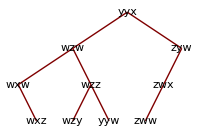
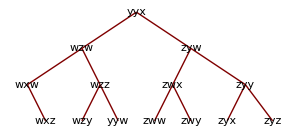
wzy(wzz)
-Graphics-
yyw,zww(zyw,zwx)
-Graphics-
zwy,zyx(zyy),zyz
-Graphics-

```mathematica
draw43
```

### 7. 已知元素个数为12的字典，其元素集合为：{ Jan, Feb, Mar, Apr, May, June, July, Aug, Sep, Oct, Nov, Dec} 按元素的次序依次插入一棵初始时为空的二叉排序树，并求其在等概率情况下检索成功的平均检索长度。

#### #code

```mathematica
d1={{Jan->Feb,Jan->Mar},{Jan->{0,1},Feb->{-1,0},Mar->{1,0}}};
d2={{Jan->Feb,Jan->Mar,Feb->Apr,Mar->May,Mar->June},
{Jan->{0,2},Feb->{-1,1},Mar->{1,1},Apr->{-2,0},June->{0,0},May->{2,0}}};
d3={{Jan->Feb,Jan->Mar,Feb->Apr,Mar->May,Mar->June,June->July,Apr->Aug,May->Sep},
{Jan->{0,2},Feb->{-2,1},Mar->{2,1},Apr->{-4,0},June->{1,0},May->{3,0},July->{0,-1},
Aug->{-3,-1},Sep->{4,-1}}};
d4={{Jan->Feb,Jan->Mar,Feb->Apr,Mar->May,Mar->June,June->July,
Apr->Aug,May->Sep,Sep->Oct,Oct->Nov,Aug->Dec},
{Jan->{0,2},Feb->{-2,1},Mar->{2,1},Apr->{-4,0},June->{1,0},May->{3,0},July->{0,-1},
Aug->{-3,-1},Sep->{4,-1},Oct->{3,-2},Nov->{2,-3},Dec->{-2,-2}}};
draw7:=Column@{"Jan, Feb, Mar",
Gplot[d1,100],
"Apr, May, June",
Gplot[d2,200],
"July, Aug, Sep",
Gplot[d3,300],
"Oct, Nov, Dec",
Gplot[d4,300]}
```

#### #draw

元素大小由字母顺序决定，而非月份的先后。

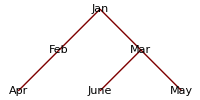
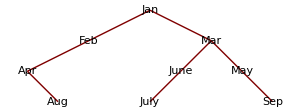
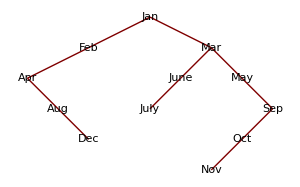
Jan, Feb, Mar
-Graphics-
Apr, May, June
-Graphics-
July, Aug, Sep
-Graphics-
Oct, Nov, Dec
-Graphics-

```mathematica
draw7
```

平均检索长度：

```mathematica
(1+2*2+3*3+4*3+5*2+6*1)/12//N
```

3.5

### 8. 按元素顺序将上题构造成AVL树，求等概率下检索成功平均检索长度

#### #code

```mathematica
f1={{"Jan^1"->"Feb^-1","Jan^1"->"Mar^-1","Feb^-1"->"Apr^0","Mar^-1"->"May^0",
"Mar^-1"->"June^-1","June^-1"->"July^0"},
{"Jan^1"->{0,2},"Feb^-1"->{-2,1},"Mar^-1"->{2,1},"Apr^0"->{-4,0},"June^-1"->{1,0},
"May^0"->{3,0},"July^0"->{0,-1}}};
f2={{"Jan^0"->"Feb^-2","Jan^0"->"Mar^-1","Feb^-2"->"Apr^1","Mar^-1"->"May^0",
"Mar^-1"->"June^-1","June^-1"->"July^0","Apr^1"->"Aug^0"},
{"Jan^0"->{0,2},"Feb^-2"->{-2,1},"Mar^-1"->{2,1},"Apr^1"->{-4,0},"June^-1"->{1,0},
"May^0"->{3,0},"July^0"->{0,-1},"Aug^0"->{-3,-1}}};
f3={{"Jan^1"->"Aug^0","Jan^1"->"Mar^-1","Aug^0"->"Feb^0","Mar^-1"->"May^0",
"Mar^-1"->"June^-1","June^-1"->"July^0","Aug^0"->"Apr^0"},
{"Jan^1"->{0,2},"Aug^0"->{-2,1},"Mar^-1"->{2,1},"Apr^0"->{-4,0},"June^-1"->{1,0},
"May^0"->{3,0},"July^0"->{0,-1},"Feb^0"->{-0.5,0}}};
f4={{"Jan^2"->"Aug^0","Jan^2"->"Mar^1","Aug^0"->"Feb^0","Mar^1"->"May^2",
"Mar^1"->"June^-1","June^-1"->"July^0","Aug^0"->"Apr^0","May^2"->"Sep^-1","Sep^-1"->"Oct^0"},
{"Jan^2"->{0,2},"Aug^0"->{-2,1},"Mar^1"->{2,1},"Apr^0"->{-3,0},"June^-1"->{1,0},
"May^2"->{3,0},"July^0"->{0,-1},"Feb^0"->{-1,0},"Sep^-1"->{4,-1},"Oct^0"->{3,-2}}};
f5={{"Jan^1"->"Aug^0","Jan^1"->"Mar^0","Aug^0"->"Feb^0","Mar^0"->"Oct^0","Mar^0"->"June^-1"
,"June^-1"->"July^0","Aug^0"->"Apr^0","Oct^0"->"Sep^0","Oct^0"->"May^0"},
{"Jan^1"->{0,2},"Aug^0"->{-2,1},"Mar^0"->{2,1},"Apr^0"->{-3,0},"June^-1"->{1,0},
"May^0"->{2,-1},"July^0"->{0,-1},"Feb^0"->{-1,0},"Sep^0"->{4,-1},"Oct^0"->{3,0}}};
f6={{"Jan^2"->"Aug^0","Jan^2"->"Mar^1","Aug^0"->"Feb^0","Mar^1"->"Oct^-1","Mar^1"->"June^-1"
,"June^-1"->"July^0","Aug^0"->"Apr^0","Oct^-1"->"Sep^0","Oct^-1"->"May^1","May^1"->"Nov^0"},
{"Jan^2"->{0,2},"Aug^0"->{-2,1},"Mar^1"->{2,1},"Apr^0"->{-3,0},"June^-1"->{1,0},
"May^1"->{2,-1},"July^0"->{0,-1},"Feb^0"->{-1,0},"Sep^0"->{4,-1},
"Oct^-1"->{3,0},"Nov^0"->{3,-2}}};
f7={{"Jan^0"->"Aug^0","Mar^0"->"Jan^0","Aug^0"->"Feb^0","Mar^0"->"Oct^-1","Jan^0"->"June^-1"
,"June^-1"->"July^0","Aug^0"->"Apr^0","Oct^-1"->"Sep^0","Oct^-1"->"May^1","May^1"->"Nov^0"},
{"Jan^0"->{-1,1},"Aug^0"->{-2,0},"Mar^0"->{1,2},"Apr^0"->{-3,-1},"June^-1"->{0.5,0},
"May^1"->{2,0},"July^0"->{0,-1},"Feb^0"->{-1.5,-1},"Sep^0"->{4,0},
"Oct^-1"->{3,1},"Nov^0"->{3,-1}}};
f8={{"Jan^-1"->"Aug^1","Mar^-1"->"Jan^-1","Aug^1"->"Feb^-1","Mar^-1"->"Oct^-1","Jan^-1"->"June^-1"
,"June^-1"->"July^0","Aug^1"->"Apr^0","Oct^-1"->"Sep^0","Oct^-1"->"May^1",
"May^1"->"Nov^0","Feb^-1"->"Dec^0"},
{"Jan^-1"->{-1,1},"Aug^1"->{-2,0},"Mar^-1"->{1,2},"Apr^0"->{-3,-1},"June^-1"->{0.5,0},
"May^1"->{2,0},"July^0"->{0,-1},"Feb^-1"->{-1.5,-1},"Sep^0"->{4,0},
"Oct^-1"->{3,1},"Nov^0"->{3,-1}},"Dec^0"->{-2,-2}};
draw8:=Column@{"Jan, Feb, Mar, Apr, May, June, July",
Gplot[f1,300],
"Aug -> exchange (Apr, Feb, Aug)",
Row@{Gplot[f2,250],"->",Gplot[f3,250]},
"Sep, Oct -> exchange (May, Sep, Oct)",
Row@{Gplot[f4,260],"->",Gplot[f5,260]},
"Nov -> exchange (Jan, June, Mar)",
Row@{Gplot[f6,260],"->",Gplot[f7,260]},
"Dec",
Gplot[f8,300]}
```

#### #draw

按7的方法构造，但当遇到平衡因子绝对值大于1，需要调整最小不平衡子树。

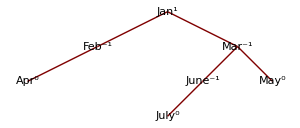
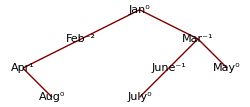
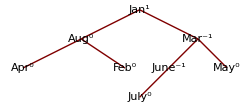
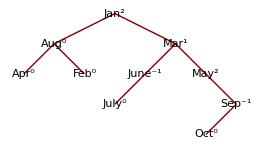
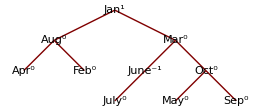
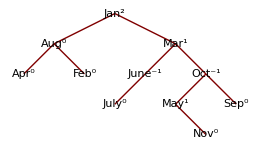
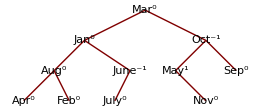
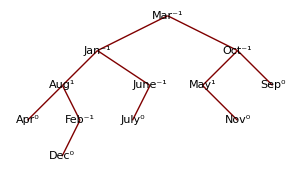
Jan, Feb, Mar, Apr, May, June, July
-Graphics-
Aug -> exchange (Apr, Feb, Aug)
-Graphics-->-Graphics-
Sep, Oct -> exchange (May, Sep, Oct)
-Graphics-->-Graphics-
Nov -> exchange (Jan, June, Mar)
-Graphics-->-Graphics-
Dec
-Graphics-

```mathematica
draw8
```

平均检索长度：

```mathematica
(1+2*2+4*3+4*4+1*5)/12//N
```

3.16667

### 9. 试给出一个个数最小的关键码序列，使构造AVL树时四种调整平衡操作(LL, LR, RR, RL)各至少执行一次，并画出其构造过程。

#### #code

```mathematica
k1={{"15^-2"->"10^-1","10^-1"->"5^0"},{"15^-2"->{2,2},"10^-1"->{1,1},"5^0"->{0,0}}};
k2={{"10^0"->"5^0","10^0"->"15^0"},{"10^0"->{0,1},"15^0"->{1,0},"5^0"->{-1,0}}};
k3={{"10^-2"->"5^2","10^-2"->"15^0","5^2"->"9^-1","9^-1"->"7^0"},
{"10^-2"->{0,1},"15^0"->{1,0},"5^2"->{-1,0},"9^-1"->{0,-1},"7^0"->{-1,-2}}};
k4={{"10^-1"->"7^0","10^-1"->"15^0","7^0"->"5^0","7^0"->"9^0"},
{"10^-1"->{0,1},"15^0"->{1,0},"7^0"->{-1,0},"9^0"->{0,-1},"5^0"->{-2,-1}}};
k5={{"10^-2"->"7^1","10^-2"->"15^0","7^1"->"5^0","7^1"->"9^-1","9^-1"->"8^0"},
{"10^-2"->{0,1},"15^0"->{1,0},"7^1"->{-1,0},"9^-1"->{0,-1},"5^0"->{-2,-1},"8^0"->{-1,-2}}};
k6={{"9^0"->"7^0","10^1"->"15^0","7^0"->"5^0","7^0"->"8^0","9^0"->"10^1"},
{"9^0"->{0,1},"10^1"->{1,0},"7^0"->{-1,0},"8^0"->{0,-1},"5^0"->{-2,-1},"15^0"->{2,-1}}};
k7={{"9^1"->"7^0","10^2"->"15^1","7^0"->"5^0","7^0"->"8^0","9^1"->"10^2","15^1"->"17^0"},
{"9^1"->{0,1},"10^2"->{1,0},"7^0"->{-1,0},"8^0"->{0,-1},
"5^0"->{-2,-1},"15^1"->{2,-1},"17^0"->{3,-2}}};
k8={{"9^0"->"7^0","15^0"->"10^0","7^0"->"5^0","7^0"->"8^0","9^0"->"15^0","15^0"->"17^0"},
{"9^0"->{0.5,1},"15^0"->{2,0},"7^0"->{-1,0},"8^0"->{0,-1},
"5^0"->{-2,-1},"10^0"->{1,-1},"17^0"->{3,-1}}};
draw9:=Row@{Gplot[k1,100]," LL →",Gplot[k2,100]," Add 9,7 →"
,Gplot[k3,100]," RL →",Gplot[k4,150]," Add 8 →",Gplot[k5,150]," LR →"
,Gplot[k6,180]," Add 17 →",Gplot[k7,200]," RR →",Gplot[k8,200]}
```

#### #draw

最小为7个

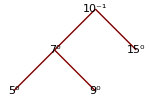
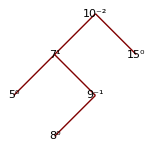
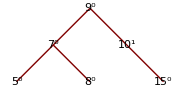
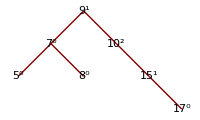
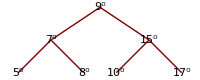
-Graphics- LL →-Graphics- Add 9,7 →-Graphics- RL →-Graphics- Add 8 →-Graphics- LR →-Graphics- Add 17 →-Graphics- RR →-Graphics-

```mathematica
draw9
```

# 第四次

## 第8章

### 1. 给出初始排序码序列为503, 017, 512, 061, 908, 170, 897, 275, 653, 426, 154, 509, 612, 677, 765, 703， 分别写出直接插入，shell，起泡，直接选择，堆，归并，基数排序的各趟运行结果。

#### #code

```mathematica
d1={503, 017, 512, 061, 908, 170, 897, 275, 653, 426, 154, 509, 612, 677, 765, 703};
dr1:=Grid[Table[(Item[#,Frame->Blue]&/@Sort[d1[[;;i]]])~Join~
{Item[d1[[i+1]],Frame->Green]}~Join~d1[[i+2;;]],{i,Length@d1-1}]~Join~
{(Item[#,Frame->Blue]&/@Sort[d1])}]

Sf2[c_,s_,o_]:=Item[#,Background->c]&/@Sort[Table[d1[[i+o]],{i,1,Length@d1,s}]]
Cf2[d_]:=Flatten@Transpose[d]
dr2:=Grid[{(Item[#,Frame->Red]&/@d1)}~Join~
Table[Cf2[Table[Sf2[RGBColor[(j+1)/i,(j+1)/i,1],i,j],{j,0,i-1}]],{i,{8,4,2,1}}],
Frame->All]

dr3:=(tmp=d1;dr3out={d1};
Do[Do[If[tmp⟦j⟧>tmp⟦j+1⟧,tmp[[{j,j+1}]]=tmp[[{j+1,j}]]],
{j,i}];AppendTo[dr3out,tmp],{i,Length@d1-1,1,-1}];
Grid[dr3out,Frame->{None,None,Table[{{i+1,i+1},{Length@dr3out-i+1,Length@dr3out}}->Blue,{i,Length@dr3out}]},
Background->{None,None,Table[{Length@d1-i+2,i}->Green,{i,Length@dr3out}]}])

dr4:=(tmp=d1;dr3out={};pos={};
Do[AppendTo[dr3out,tmp];
AppendTo[pos,Position[tmp[[i;;]],Min[tmp[[i;;]]]]];tmp[[{i,pos[[i,1,1]]+i-1}]]=tmp[[{pos[[i,1,1]]+i-1,i}]],{i,Length@d1}];
Grid[dr3out,Frame->{None,None,Table[{{i,i},{1,i-1}}->Blue,{i,Length@dr3out}]},
Background->{None,None,Flatten[Table[{{i-1,i-1}->Green,{i,pos[[i,1,1]]+i-1}->Red},{i,Length@dr3out}],1]}])

get[data_,i_]:=If[2i+1≤Length@data,{#[[i]]->#[[2i]],#[[i]]->#[[2i+1]]}&@data,{#[[i]]->#[[2i]]}&@data]
dr5s[data_]:=TreePlot[Flatten@Table[get[data,i],{i,IntegerPart[Length@data/2]}],VertexLabeling->True,ImageSize->300]
dr5l[data_]:=Grid[{data},Frame->All,Background->{None,None,Table[{{1,1},{2i,2i+1}}->RGBColor[(8-i)/8,i/8,0],{i,8}]}]
dr5d[data_,i_]:=Grid[{data[[i]]},Frame->All,
Background->{None,None,{{{1,1},{9-i,9-i}}->Red,{{1,1},{2(9-i),2(9-i)}}->Green,{{1,1},{2(9-i)+1,2(9-i)+1}}->Green}}]
shf[i_]:=If[2i+1≤Length@tmp,
If[tmp[[2i]]>tmp[[2i+1]],If[tmp[[i]]<tmp[[2i]],tmp[[{i,2i}]]=tmp[[{2i,i}]]],
If[tmp[[i]]<tmp[[2i+1]],tmp[[{i,2i+1}]]=tmp[[{2i+1,i}]]]],
If[tmp[[i]]<tmp[[2i]],tmp[[{i,2i}]]=tmp[[{2i,i}]]]]

dr5:=(tmp=d1;dr5out={d1};Do[Do[shf[j],{j,i,8}];AppendTo[dr5out,tmp],{i,8,1,-1}];
Column[Flatten[Table[{dr5s[dr5out[[i]]]}~Join~{dr5d[dr5out,i]}
,{i,Length@dr5out}]]])
dr52:=(tmp=dr5out[[-1]];dr5sort={};dr5out2={};dr5out3={};
Do[PrependTo[dr5sort,tmp[[1]]];tmp[[1]]=tmp[[-1]];tmp=Delete[tmp,Length@tmp];AppendTo[dr5out2,tmp];
Do[Do[shf[j],{j,ii,IntegerPart[Length@tmp/2]}],{ii,IntegerPart[Length@tmp/2]}];AppendTo[dr5out3,tmp],{i,Length@d1}];
Column[Flatten[Table[{Row[{dr5s[dr5out2[[i]]],dr5s[dr5out3[[i]]]}]}~Join~{Grid[{dr5out2[[i]]~Join~(
Item[#,Frame->Blue]&/@dr5sort[[Length@dr5out2-i+1;;]])},Frame->All]},{i,Length@dr5out2-1}]]])

dr6:=(tmp=d1;dr6out={d1};
Do[tmp=Flatten[Table[Sort[tmp[[2^j*(i-1)+1;;2^j*i]]],{i,IntegerPart[Length@d1/2^j]}]];AppendTo[dr6out,tmp],{j,1,IntegerPart[Log2[Length@d1]]}];
Grid[dr6out,Frame->{True,{Red},Flatten[Table[Table[{{j+1,j+1},{2^j*(i-1)+1,2^j*i}}->Blue,{i,IntegerPart[Length@d1/2^j]}],
{j,1,IntegerPart[Log2[Length@d1]]}],1]}])

dr7:=(tmp=d1;dr7out={};Do[AppendTo[dr7out,Table[Select[tmp,Mod[IntegerPart[#/10^(i-1)],10]==j&],{j,0,9}]];tmp=Flatten[dr7out[[i]]],{i,3}];
Grid[{{"Initial",Grid[{d1},Frame->Red]}}~Join~
Table[{Grid[Table[{"["~~ToString@j~~"]"}~Join~dr7out[[i,j+1]],{j,0,9}],Frame->All,Background->{{Red}}],Grid[{Flatten@dr7out[[i]]}]},{i,3}]])
```

#### #draw

直接插入排序：

```mathematica
dr1
```

503 | 17 | 512 | 61 | 908 | 170 | 897 | 275 | 653 | 426 | 154 | 509 | 612 | 677 | 765 | 703
17 | 503 | 512 | 61 | 908 | 170 | 897 | 275 | 653 | 426 | 154 | 509 | 612 | 677 | 765 | 703
17 | 503 | 512 | 61 | 908 | 170 | 897 | 275 | 653 | 426 | 154 | 509 | 612 | 677 | 765 | 703
17 | 61 | 503 | 512 | 908 | 170 | 897 | 275 | 653 | 426 | 154 | 509 | 612 | 677 | 765 | 703
17 | 61 | 503 | 512 | 908 | 170 | 897 | 275 | 653 | 426 | 154 | 509 | 612 | 677 | 765 | 703
17 | 61 | 170 | 503 | 512 | 908 | 897 | 275 | 653 | 426 | 154 | 509 | 612 | 677 | 765 | 703
17 | 61 | 170 | 503 | 512 | 897 | 908 | 275 | 653 | 426 | 154 | 509 | 612 | 677 | 765 | 703
17 | 61 | 170 | 275 | 503 | 512 | 897 | 908 | 653 | 426 | 154 | 509 | 612 | 677 | 765 | 703
17 | 61 | 170 | 275 | 503 | 512 | 653 | 897 | 908 | 426 | 154 | 509 | 612 | 677 | 765 | 703
17 | 61 | 170 | 275 | 426 | 503 | 512 | 653 | 897 | 908 | 154 | 509 | 612 | 677 | 765 | 703
17 | 61 | 154 | 170 | 275 | 426 | 503 | 512 | 653 | 897 | 908 | 509 | 612 | 677 | 765 | 703
17 | 61 | 154 | 170 | 275 | 426 | 503 | 509 | 512 | 653 | 897 | 908 | 612 | 677 | 765 | 703
17 | 61 | 154 | 170 | 275 | 426 | 503 | 509 | 512 | 612 | 653 | 897 | 908 | 677 | 765 | 703
17 | 61 | 154 | 170 | 275 | 426 | 503 | 509 | 512 | 612 | 653 | 677 | 897 | 908 | 765 | 703
17 | 61 | 154 | 170 | 275 | 426 | 503 | 509 | 512 | 612 | 653 | 677 | 765 | 897 | 908 | 703
17 | 61 | 154 | 170 | 275 | 426 | 503 | 509 | 512 | 612 | 653 | 677 | 703 | 765 | 897 | 908

Shell排序 (d_1=8) :

```mathematica
dr2
```

503 | 17 | 512 | 61 | 908 | 170 | 897 | 275 | 653 | 426 | 154 | 509 | 612 | 677 | 765 | 703
503 | 17 | 154 | 61 | 612 | 170 | 765 | 275 | 653 | 426 | 512 | 509 | 908 | 677 | 897 | 703
503 | 17 | 154 | 61 | 612 | 170 | 512 | 275 | 653 | 426 | 765 | 509 | 908 | 677 | 897 | 703
154 | 17 | 503 | 61 | 512 | 170 | 612 | 275 | 653 | 426 | 765 | 509 | 897 | 677 | 908 | 703
17 | 61 | 154 | 170 | 275 | 426 | 503 | 509 | 512 | 612 | 653 | 677 | 703 | 765 | 897 | 908

起泡排序

```mathematica
dr3
```

503 | 17 | 512 | 61 | 908 | 170 | 897 | 275 | 653 | 426 | 154 | 509 | 612 | 677 | 765 | 703
17 | 503 | 61 | 512 | 170 | 897 | 275 | 653 | 426 | 154 | 509 | 612 | 677 | 765 | 703 | 908
17 | 61 | 503 | 170 | 512 | 275 | 653 | 426 | 154 | 509 | 612 | 677 | 765 | 703 | 897 | 908
17 | 61 | 170 | 503 | 275 | 512 | 426 | 154 | 509 | 612 | 653 | 677 | 703 | 765 | 897 | 908
17 | 61 | 170 | 275 | 503 | 426 | 154 | 509 | 512 | 612 | 653 | 677 | 703 | 765 | 897 | 908
17 | 61 | 170 | 275 | 426 | 154 | 503 | 509 | 512 | 612 | 653 | 677 | 703 | 765 | 897 | 908
17 | 61 | 170 | 275 | 154 | 426 | 503 | 509 | 512 | 612 | 653 | 677 | 703 | 765 | 897 | 908
17 | 61 | 170 | 154 | 275 | 426 | 503 | 509 | 512 | 612 | 653 | 677 | 703 | 765 | 897 | 908
17 | 61 | 154 | 170 | 275 | 426 | 503 | 509 | 512 | 612 | 653 | 677 | 703 | 765 | 897 | 908
17 | 61 | 154 | 170 | 275 | 426 | 503 | 509 | 512 | 612 | 653 | 677 | 703 | 765 | 897 | 908
17 | 61 | 154 | 170 | 275 | 426 | 503 | 509 | 512 | 612 | 653 | 677 | 703 | 765 | 897 | 908
17 | 61 | 154 | 170 | 275 | 426 | 503 | 509 | 512 | 612 | 653 | 677 | 703 | 765 | 897 | 908
17 | 61 | 154 | 170 | 275 | 426 | 503 | 509 | 512 | 612 | 653 | 677 | 703 | 765 | 897 | 908
17 | 61 | 154 | 170 | 275 | 426 | 503 | 509 | 512 | 612 | 653 | 677 | 703 | 765 | 897 | 908
17 | 61 | 154 | 170 | 275 | 426 | 503 | 509 | 512 | 612 | 653 | 677 | 703 | 765 | 897 | 908
17 | 61 | 154 | 170 | 275 | 426 | 503 | 509 | 512 | 612 | 653 | 677 | 703 | 765 | 897 | 908

直接选择排序

```mathematica
dr4
```

503 | 17 | 512 | 61 | 908 | 170 | 897 | 275 | 653 | 426 | 154 | 509 | 612 | 677 | 765 | 703
17 | 503 | 512 | 61 | 908 | 170 | 897 | 275 | 653 | 426 | 154 | 509 | 612 | 677 | 765 | 703
17 | 61 | 512 | 503 | 908 | 170 | 897 | 275 | 653 | 426 | 154 | 509 | 612 | 677 | 765 | 703
17 | 61 | 154 | 503 | 908 | 170 | 897 | 275 | 653 | 426 | 512 | 509 | 612 | 677 | 765 | 703
17 | 61 | 154 | 170 | 908 | 503 | 897 | 275 | 653 | 426 | 512 | 509 | 612 | 677 | 765 | 703
17 | 61 | 154 | 170 | 275 | 503 | 897 | 908 | 653 | 426 | 512 | 509 | 612 | 677 | 765 | 703
17 | 61 | 154 | 170 | 275 | 426 | 897 | 908 | 653 | 503 | 512 | 509 | 612 | 677 | 765 | 703
17 | 61 | 154 | 170 | 275 | 426 | 503 | 908 | 653 | 897 | 512 | 509 | 612 | 677 | 765 | 703
17 | 61 | 154 | 170 | 275 | 426 | 503 | 509 | 653 | 897 | 512 | 908 | 612 | 677 | 765 | 703
17 | 61 | 154 | 170 | 275 | 426 | 503 | 509 | 512 | 897 | 653 | 908 | 612 | 677 | 765 | 703
17 | 61 | 154 | 170 | 275 | 426 | 503 | 509 | 512 | 612 | 653 | 908 | 897 | 677 | 765 | 703
17 | 61 | 154 | 170 | 275 | 426 | 503 | 509 | 512 | 612 | 653 | 908 | 897 | 677 | 765 | 703
17 | 61 | 154 | 170 | 275 | 426 | 503 | 509 | 512 | 612 | 653 | 677 | 897 | 908 | 765 | 703
17 | 61 | 154 | 170 | 275 | 426 | 503 | 509 | 512 | 612 | 653 | 677 | 703 | 908 | 765 | 897
17 | 61 | 154 | 170 | 275 | 426 | 503 | 509 | 512 | 612 | 653 | 677 | 703 | 765 | 908 | 897
17 | 61 | 154 | 170 | 275 | 426 | 503 | 509 | 512 | 612 | 653 | 677 | 703 | 765 | 897 | 908

堆排序

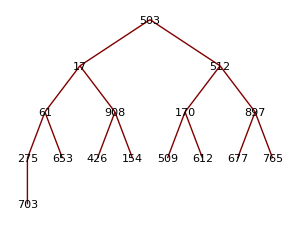
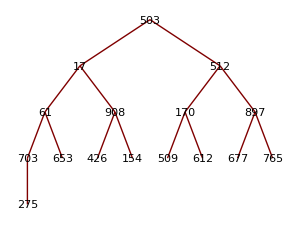
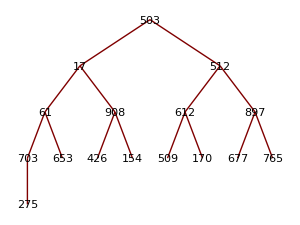
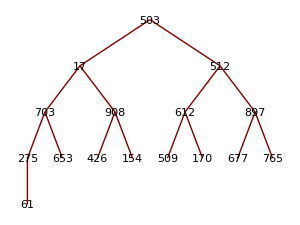
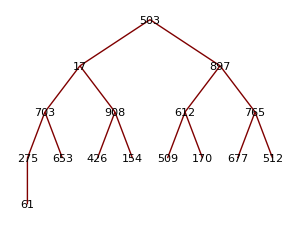
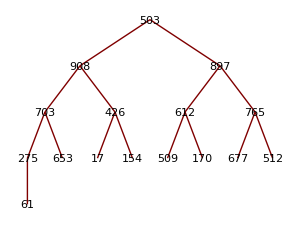
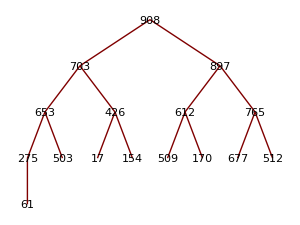
-Graphics-
503 | 17 | 512 | 61 | 908 | 170 | 897 | 275 | 653 | 426 | 154 | 509 | 612 | 677 | 765 | 703
-Graphics-
503 | 17 | 512 | 61 | 908 | 170 | 897 | 703 | 653 | 426 | 154 | 509 | 612 | 677 | 765 | 275
-Graphics-
503 | 17 | 512 | 61 | 908 | 170 | 897 | 703 | 653 | 426 | 154 | 509 | 612 | 677 | 765 | 275
-Graphics-
503 | 17 | 512 | 61 | 908 | 612 | 897 | 703 | 653 | 426 | 154 | 509 | 170 | 677 | 765 | 275
-Graphics-
503 | 17 | 512 | 61 | 908 | 612 | 897 | 703 | 653 | 426 | 154 | 509 | 170 | 677 | 765 | 275
-Graphics-
503 | 17 | 512 | 703 | 908 | 612 | 897 | 275 | 653 | 426 | 154 | 509 | 170 | 677 | 765 | 61
-Graphics-
503 | 17 | 897 | 703 | 908 | 612 | 765 | 275 | 653 | 426 | 154 | 509 | 170 | 677 | 512 | 61
-Graphics-
503 | 908 | 897 | 703 | 426 | 612 | 765 | 275 | 653 | 17 | 154 | 509 | 170 | 677 | 512 | 61
-Graphics-
908 | 703 | 897 | 653 | 426 | 612 | 765 | 275 | 503 | 17 | 154 | 509 | 170 | 677 | 512 | 61

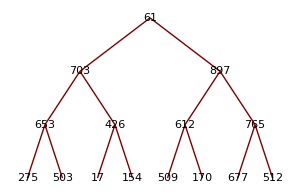
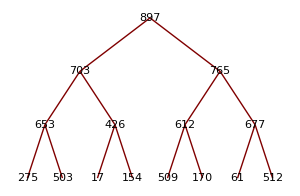
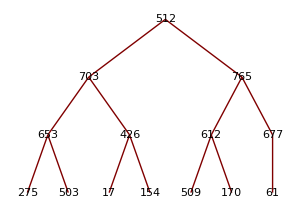
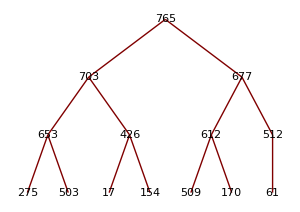
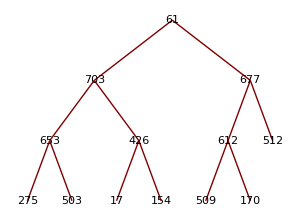
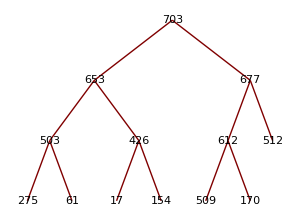
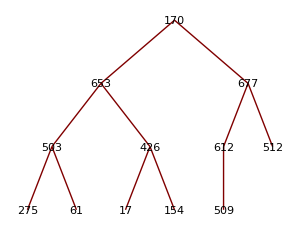
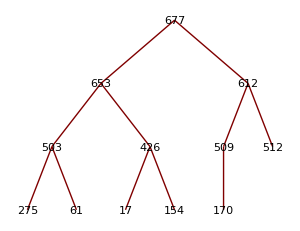
-Graphics--Graphics-
61 | 703 | 897 | 653 | 426 | 612 | 765 | 275 | 503 | 17 | 154 | 509 | 170 | 677 | 512 | 908
-Graphics--Graphics-
512 | 703 | 765 | 653 | 426 | 612 | 677 | 275 | 503 | 17 | 154 | 509 | 170 | 61 | 897 | 908
-Graphics--Graphics-
61 | 703 | 677 | 653 | 426 | 612 | 512 | 275 | 503 | 17 | 154 | 509 | 170 | 765 | 897 | 908
-Graphics--Graphics-
170 | 653 | 677 | 503 | 426 | 612 | 512 | 275 | 61 | 17 | 154 | 509 | 703 | 765 | 897 | 908
-Graphics--Graphics-
170 | 653 | 612 | 503 | 426 | 509 | 512 | 275 | 61 | 17 | 154 | 677 | 703 | 765 | 897 | 908
-Graphics--Graphics-
154 | 503 | 612 | 275 | 426 | 509 | 512 | 170 | 61 | 17 | 653 | 677 | 703 | 765 | 897 | 908
-Graphics--Graphics-
17 | 503 | 512 | 275 | 426 | 509 | 154 | 170 | 61 | 612 | 653 | 677 | 703 | 765 | 897 | 908
-Graphics--Graphics-
61 | 503 | 509 | 275 | 426 | 17 | 154 | 170 | 512 | 612 | 653 | 677 | 703 | 765 | 897 | 908
-Graphics--Graphics-
170 | 503 | 154 | 275 | 426 | 17 | 61 | 509 | 512 | 612 | 653 | 677 | 703 | 765 | 897 | 908
-Graphics--Graphics-
61 | 426 | 154 | 275 | 170 | 17 | 503 | 509 | 512 | 612 | 653 | 677 | 703 | 765 | 897 | 908
-Graphics--Graphics-
17 | 275 | 154 | 61 | 170 | 426 | 503 | 509 | 512 | 612 | 653 | 677 | 703 | 765 | 897 | 908
-Graphics--Graphics-
17 | 170 | 154 | 61 | 275 | 426 | 503 | 509 | 512 | 612 | 653 | 677 | 703 | 765 | 897 | 908
-Graphics--Graphics-
17 | 61 | 154 | 170 | 275 | 426 | 503 | 509 | 512 | 612 | 653 | 677 | 703 | 765 | 897 | 908
-Graphics--Graphics-
17 | 61 | 154 | 170 | 275 | 426 | 503 | 509 | 512 | 612 | 653 | 677 | 703 | 765 | 897 | 908
-Graphics--Graphics-
17 | 61 | 154 | 170 | 275 | 426 | 503 | 509 | 512 | 612 | 653 | 677 | 703 | 765 | 897 | 908

```mathematica
dr5
dr52
```

归并排序

```mathematica
dr6
```

503 | 17 | 512 | 61 | 908 | 170 | 897 | 275 | 653 | 426 | 154 | 509 | 612 | 677 | 765 | 703
17 | 503 | 61 | 512 | 170 | 908 | 275 | 897 | 426 | 653 | 154 | 509 | 612 | 677 | 703 | 765
17 | 61 | 503 | 512 | 170 | 275 | 897 | 908 | 154 | 426 | 509 | 653 | 612 | 677 | 703 | 765
17 | 61 | 170 | 275 | 503 | 512 | 897 | 908 | 154 | 426 | 509 | 612 | 653 | 677 | 703 | 765
17 | 61 | 154 | 170 | 275 | 426 | 503 | 509 | 512 | 612 | 653 | 677 | 703 | 765 | 897 | 908

基数排序 (取10为基数，共3次分配)

```mathematica
dr7
```

Initial | 503 | 17 | 512 | 61 | 908 | 170 | 897 | 275 | 653 | 426 | 154 | 509 | 612 | 677 | 765 | 703
[0] | 170 |  | 
[1] | 61 |  | 
[2] | 512 | 612 | 
[3] | 503 | 653 | 703
[4] | 154 |  | 
[5] | 275 | 765 | 
[6] | 426 |  | 
[7] | 17 | 897 | 677
[8] | 908 |  | 
[9] | 509 |  |  | 170 | 61 | 512 | 612 | 503 | 653 | 703 | 154 | 275 | 765 | 426 | 17 | 897 | 677 | 908 | 509
[0] | 503 | 703 | 908 | 509
[1] | 512 | 612 | 17 | 
[2] | 426 |  |  | 
[3] |  |  |  | 
[4] |  |  |  | 
[5] | 653 | 154 |  | 
[6] | 61 | 765 |  | 
[7] | 170 | 275 | 677 | 
[8] |  |  |  | 
[9] | 897 |  |  |  | 503 | 703 | 908 | 509 | 512 | 612 | 17 | 426 | 653 | 154 | 61 | 765 | 170 | 275 | 677 | 897
[0] | 17 | 61 | 
[1] | 154 | 170 | 
[2] | 275 |  | 
[3] |  |  | 
[4] | 426 |  | 
[5] | 503 | 509 | 512
[6] | 612 | 653 | 677
[7] | 703 | 765 | 
[8] | 897 |  | 
[9] | 908 |  |  | 17 | 61 | 154 | 170 | 275 | 426 | 503 | 509 | 512 | 612 | 653 | 677 | 703 | 765 | 897 | 908

### 5. 为下面各种情况选择合适的排序算法：

#### #code

```mathematica
list={{"方法","最小移动","最大移动","平均移动","最小比较","最大比较","平均比较","格外空间","稳定性"},
{"直接插入排序","O(n)","O(n^2)","O(n^2)","O(n)","O(n^2)","O(n^2)","O(1)","稳定"},
{"二分法插入排序","O(n)","O(n^2)","O(n^2)","O(nlog_2n)","O(nlog_2n)","O(nlog_2n)","O(1)","稳定"},
{"表插入排序","0","0","0","O(n)","O(n^2)","O(n^2)","O(n)","稳定"},
{"Shell排序","","","O(n^1.3)","","","O(n^1.3)","O(1)","不稳定"},
{"直接选择排序","0","O(n)","O(n)","O(n^2)","O(n^2)","O(n^2)","O(1)","不稳定"},
{"堆排序","","","","O(nlog_2n)","O(nlog_2n)","O(nlog_2n)","O(1)","不稳定"},
{"起泡排序","0","O(n^2)","O(n^2)","O(n)","O(n^2)","O(n^2)","O(1)","稳定"},
{"快速排序","O(nlog_2n)","O(n^2)","O(nlog_2n)","O(nlog_2n)","O(n^2)","O(nlog_2n)","O(log_2n)","不稳定"},
{"基数排序","","","","","","","O(r+n)","稳定"},
{"归并排序","","","O(nlog_2n)","","","O(nlog_2n)","O(n)","稳定"}};
```

#### #draw

```mathematica
Grid@list
```

方法 | 最小移动 | 最大移动 | 平均移动 | 最小比较 | 最大比较 | 平均比较 | 格外空间 | 稳定性
直接插入排序 | O(n) | O(n^2) | O(n^2) | O(n) | O(n^2) | O(n^2) | O(1) | 稳定
二分法插入排序 | O(n) | O(n^2) | O(n^2) | O(nlog_2n) | O(nlog_2n) | O(nlog_2n) | O(1) | 稳定
表插入排序 | 0 | 0 | 0 | O(n) | O(n^2) | O(n^2) | O(n) | 稳定
Shell排序 |  |  | O(n^1.3) |  |  | O(n^1.3) | O(1) | 不稳定
直接选择排序 | 0 | O(n) | O(n) | O(n^2) | O(n^2) | O(n^2) | O(1) | 不稳定
堆排序 |  |  |  | O(nlog_2n) | O(nlog_2n) | O(nlog_2n) | O(1) | 不稳定
起泡排序 | 0 | O(n^2) | O(n^2) | O(n) | O(n^2) | O(n^2) | O(1) | 稳定
快速排序 | O(nlog_2n) | O(n^2) | O(nlog_2n) | O(nlog_2n) | O(n^2) | O(nlog_2n) | O(log_2n) | 不稳定
基数排序 |  |  |  |  |  |  | O(r+n) | 稳定
归并排序 |  |  | O(nlog_2n) |  |  | O(nlog_2n) | O(n) | 稳定

#### (1) n=30, 且要求最坏情况下速度最快；

n较小时，算法简单的速度较快，可用直接插入，直接选择，起泡排序，直接选择的最大移动次数较少，可能最快。

#### (2) n=30, 且要求既要快，又要排序稳定；

可用直接插入或起泡排序。

#### (3) n=1000, 要求平均情况下速度最快；

快速排序，堆排序，归并排序

#### (4) n=1000, 要求最坏情况下速度最快；

堆排序，归并排序

#### (5) n=1000, 要求既要快，又要最节省存储空间;

堆排序

### 算法3，设计一个有效的算法，在1000个无序的元素中，挑选出其中前5个最大的元素。

// 直接选择排序法，比较~5n次。
template <typename Data> void max5(int n, Data *list, Data result[5]) {
  for (int i=0;i<5;i++)  {
    result[i]=list[i]; 
    int position=0;     // For saving position of maximum element
    for (int j=i+1;j<n;j++) {
      if (result[i]<list[j]) {
        result[i]=list[j];   // Select maximum, store in result[i]
        position=j;
      }
    }
    list[position]=list[i];  // exchange i element with maximum element in range (i->end)
  }
}

### 算法7， 试编写一个将一组英文单词按字典序排列的基数排序算法。设单词均由大写字母构成，最长的单词有d个字母。

// Link List structure =========================//
template <typename Data>
struct ListMember{
  Data info;
  ListMember *next;

  //constructor=======================================//
  ListMember(const Data i): info(i), next(0) {}
  
  //destructor========================================//
  ~ListMember() {
    if (next) delete next;
    next=0;
    info=0;
  }
};

template <typename Data> struct ListHeader{
  ListMember<Data> *p;
  ListMember<Data> *last;
  int n;

  //constructor=======================================//  
  ListHeader(): p(0), last(0), n(0) {}

  //destructor========================================//
  ~ListHeader() {
    if (p) delete p;
  }

  //Clear all data====================================//
  void reset() {
    if (p) delete p;
    p=0;
    last=0;
    n=0;
  }
  
  //Add new member at the end=========================//
  void push_back(const Data i){
    if (!n) {
      p=new ListMember<Data>(i);
      last=p;
      n++;
    }
    else{
      ListMember<Data> *inew=new ListMember<Data>(i);
      last->next=inew;
      last=inew;
      n++;
    }
  }
};

// Word sort function ==================================//
void word_sort(const int n, const int d, char* list[]){  
  //Here the char* in list have length word max-length(d)+1=//
  //27 Link List to select the different char===============//
  ListHeader<char*> dlist[27];    
  //Store the length of word in the last element of array===//
  for (int j=0;j<n;j++) list[j][d]=strlen(list[j]);
  //Main loop for sort =====================================//
  for (int i=0;i<d;i++) {
    //divide list elements to dlist ========================//
    for (int j=0;j<n;j++){
      if (list[j][d]<d-i)
        dlist[0].push_back(list[j]);   //dlist[0] for store the words length less then d-i
      else{
        //Assume (int)A-Z is continual======================//
        int index=list[j][d-i-1]-'A'+1; 
        assert(index<27);        //For safety, check whether the char is inside 'A-Z', need include <cassert>
        assert(index>0);    
        dlist[index].push_back(list[j]);
      }
    }
    //Get back data from dlist to list =====================//
    int counts=0;
    for (int j=0;j<27;j++) {
      ListMember<char*> *di=dlist[j].p;
      while (di) {
        list[counts++]=di->info;
        di=di->next;
      }
      dlist[j].reset();     //Clear dlist for new loop
    }
  }
}

## 第9章

### 6. 对于图9.26 所示的网络，请分别用Prim算法和Kruskal算法构造该网络的最小生成树

#### #code

```mathematica
edgematrix={{∞,2,3,∞,∞,∞,∞,∞},{2,∞,∞,2,∞,∞,∞,∞},{3,∞,∞,1,∞,∞,∞,∞},{∞,2,1,∞,2,4,∞,∞},
{∞,∞,∞,2,∞,1,2,∞},{∞,∞,∞,4,1,∞,2,1},{∞,∞,∞,∞,2,2,∞,1},{∞,∞,∞,∞,∞,1,1,∞}};
vertex={v0,v1,v2,v3,v4,v5,v6,v7};
mst=Table[{1,i,edgematrix[[1,i]]},{i,2,Length@vertex}];
U={1};mstlst={mst};
Do[pos=Select[Position[mst[[i;;,3]],Min[mst[[i;;,3]]]],Length@#==1&][[1,1]];mst[[{i,pos+i-1}]]=mst[[{pos+i-1,i}]];AppendTo[U,mst[[i,2]]];AppendTo[mstlst,mst];
Do[jj=mst[[j,2]];pos2=Select[Position[edgematrix[[All,jj]],Min[edgematrix[[U,jj]]]],Length@#==1&][[1,1]];mst[[j]]={pos2,jj,edgematrix[[jj,pos2]]},{j,i+1,7}];
AppendTo[mstlst,mst],{i,7}];
linklst=Table[{vertex[[mstlst[[i,j,1]]]],vertex[[mstlst[[i,j,2]]]],mstlst[[i,j,3]]},{i,Length@mstlst},{j,Length@mstlst[[1]]}];
d61:=Column@{GraphPlot[{{v0->v1,2},{v1->v3,2},{v0->v2,3},{v2->v3,1},{v3->v4,2},{v3->v5,4},{v4->v5,1},{v4->v6,2},{v5->v6,2},{v5->v7,1},{v6->v7,1}},
VertexLabeling->True,ImageSize->400],
(Table[edgematrix[[i,i]]=0,{i,Length@edgematrix}];Grid[edgematrix,Frame->All]),
Grid[linklst,Frame->{None,{Green},Flatten[Table[{{{2i,2i+1},{i,i}}->Blue,{{2i+1,2i+1},{i+1,Length@mstlst[[1]]}}->Red},{i,Length@mstlst-1}]]}],
GraphPlot[Table[{linklst[[-1,i,1]]->linklst[[-1,i,2]],linklst[[-1,i,3]]},{i,Length@linklst[[1]]}],VertexLabeling->True,ImageSize->300]}

edgelst=Select[Flatten[Table[{vertex[[i]]<->vertex[[j]],edgematrix[[i,j]]},{i,Length@edgematrix},{j,i+1,Length@edgematrix}],1],#[[2]]≠∞&&#[[2]]≠0&];
nlen=Length@edgelst;
graphlst={};glst={};
Do[tmp=Select[Position[edgelst[[All,2]],Min[edgelst[[All,2]]]],Length@#==1&][[1,1]];AppendTo[graphlst,edgelst[[tmp]]];
AppendTo[glst,{ToString@edgelst[[tmp,1]],Graph[Table[Labeled[graphlst[[i,1]],graphlst[[i,2]]],{i,Length@graphlst}],VertexLabels->"Name",ImageSize->200]}];
If[AcyclicGraphQ[Graph[graphlst[[All,1]]]],glst[[-1,1]]="Add "~~glst[[-1,1]],glst[[-1,1]]="Cyclic Graph with "~~glst[[-1,1]];
graphlst=Delete[graphlst,Length@graphlst]];
edgelst=Delete[edgelst,tmp],{i,nlen}];AppendTo[glst,{"Finished",Graph[Table[Labeled[graphlst[[i,1]],graphlst[[i,2]]],{i,Length@graphlst}],VertexLabels->"Name",ImageSize->200]}];
d62:=Row[Column[#,Center]&/@glst,"  "]
```

#### #draw

Prim

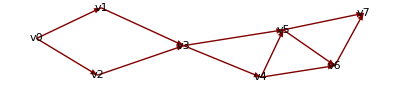
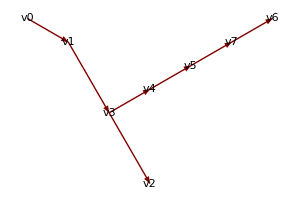
-Graphics-
0 | 2 | 3 | ∞ | ∞ | ∞ | ∞ | ∞
2 | 0 | ∞ | 2 | ∞ | ∞ | ∞ | ∞
3 | ∞ | 0 | 1 | ∞ | ∞ | ∞ | ∞
∞ | 2 | 1 | 0 | 2 | 4 | ∞ | ∞
∞ | ∞ | ∞ | 2 | 0 | 1 | 2 | ∞
∞ | ∞ | ∞ | 4 | 1 | 0 | 2 | 1
∞ | ∞ | ∞ | ∞ | 2 | 2 | 0 | 1
∞ | ∞ | ∞ | ∞ | ∞ | 1 | 1 | 0
{v0,v1,2} | {v0,v2,3} | {v0,v3,∞} | {v0,v4,∞} | {v0,v5,∞} | {v0,v6,∞} | {v0,v7,∞}
{v0,v1,2} | {v0,v2,3} | {v0,v3,∞} | {v0,v4,∞} | {v0,v5,∞} | {v0,v6,∞} | {v0,v7,∞}
{v0,v1,2} | {v0,v2,3} | {v1,v3,2} | {v0,v4,∞} | {v0,v5,∞} | {v0,v6,∞} | {v0,v7,∞}
{v0,v1,2} | {v1,v3,2} | {v0,v2,3} | {v0,v4,∞} | {v0,v5,∞} | {v0,v6,∞} | {v0,v7,∞}
{v0,v1,2} | {v1,v3,2} | {v3,v2,1} | {v3,v4,2} | {v3,v5,4} | {v0,v6,∞} | {v0,v7,∞}
{v0,v1,2} | {v1,v3,2} | {v3,v2,1} | {v3,v4,2} | {v3,v5,4} | {v0,v6,∞} | {v0,v7,∞}
{v0,v1,2} | {v1,v3,2} | {v3,v2,1} | {v3,v4,2} | {v3,v5,4} | {v0,v6,∞} | {v0,v7,∞}
{v0,v1,2} | {v1,v3,2} | {v3,v2,1} | {v3,v4,2} | {v3,v5,4} | {v0,v6,∞} | {v0,v7,∞}
{v0,v1,2} | {v1,v3,2} | {v3,v2,1} | {v3,v4,2} | {v4,v5,1} | {v4,v6,2} | {v0,v7,∞}
{v0,v1,2} | {v1,v3,2} | {v3,v2,1} | {v3,v4,2} | {v4,v5,1} | {v4,v6,2} | {v0,v7,∞}
{v0,v1,2} | {v1,v3,2} | {v3,v2,1} | {v3,v4,2} | {v4,v5,1} | {v4,v6,2} | {v5,v7,1}
{v0,v1,2} | {v1,v3,2} | {v3,v2,1} | {v3,v4,2} | {v4,v5,1} | {v5,v7,1} | {v4,v6,2}
{v0,v1,2} | {v1,v3,2} | {v3,v2,1} | {v3,v4,2} | {v4,v5,1} | {v5,v7,1} | {v7,v6,1}
{v0,v1,2} | {v1,v3,2} | {v3,v2,1} | {v3,v4,2} | {v4,v5,1} | {v5,v7,1} | {v7,v6,1}
{v0,v1,2} | {v1,v3,2} | {v3,v2,1} | {v3,v4,2} | {v4,v5,1} | {v5,v7,1} | {v7,v6,1}
-Graphics-

```mathematica
d61
```

Kruskal

```mathematica
d62
```

Add v2 <-> v3
-Graphics-Add v4 <-> v5
-Graphics-Add v5 <-> v7
-Graphics-Add v6 <-> v7
-Graphics-Add v0 <-> v1
-Graphics-Add v1 <-> v3
-Graphics-Add v3 <-> v4
-Graphics-Cyclic Graph with v4 <-> v6
-Graphics-Cyclic Graph with v5 <-> v6
-Graphics-Cyclic Graph with v0 <-> v2
-Graphics-Cyclic Graph with v3 <-> v5
-Graphics-Finished
-Graphics-

### 7. 用Dijstra 算法求图9.27 中从顶点v_0到其他各顶点的最短路径，要求写出此图的关系矩阵arcs和数组Dist在算法执行过程中的变化，以及每一条最短路径。

#### #code

```mathematica
directmatrix={{∞,20,15,∞,∞,∞},{2,∞,∞,∞,10,30},{∞,4,∞,∞,∞,10},{∞,∞,∞,∞,∞,∞},{∞,∞,∞,15,∞,10},{∞,∞,∞,4,∞,∞}};
vertex={v0,v1,v2,v3,v4,v5};
d7d=WeightedAdjacencyGraph[vertex,directmatrix,DirectedEdges->True,VertexLabels->"Name",
EdgeLabels->Table[#[[ii,1]]->#[[ii,2]],{ii,Length@#}]&@(Select[Flatten[Table[{vertex[[i]]->vertex[[j]],directmatrix[[i,j]]},
{i,Length@directmatrix},{j,Length@directmatrix}],1]
,#[[2]]≠∞&&#[[2]]≠0&]),ImagePadding->10,ImageSize->300];
Do[directmatrix[[i,i]]=1,{i,2,Length@directmatrix}]
directmatrix[[1,1]]=0;
dmlst={Grid[directmatrix,Frame->All]};
dist=Table[{directmatrix[[1,i]],1},{i,Length@directmatrix[[1]]}];
ddlst={Grid@{Table[{dist[[i,1]],vertex[[dist[[i,2]]]]},{i,Length@dist}]}};
Do[V={};U={};Do[If[directmatrix[[i,i]]==1,AppendTo[V,i],AppendTo[U,i]],{i,Length@directmatrix}];
pos=Select[Position[dist[[All,1]],Min[dist[[V,1]]]],Length@#==1&][[1,1]];directmatrix[[pos,pos]]=0;AppendTo[dmlst,Grid[directmatrix,Frame->All]];
Do[Do[If[tmp=dist[[U[[j]],1]]+directmatrix[[U[[j]],V[[i]]]];dist[[V[[i]],1]]>tmp,dist[[V[[i]]]]={tmp,U[[j]]}],{j,Length@U}],{i,Length@V}];
AppendTo[ddlst,Grid@{Table[{dist[[jj,1]],vertex[[dist[[jj,2]]]]},{jj,Length@dist}]}],{i,Length@directmatrix-1}]
plist={};Do[flag=i;path={};While[flag≠1,PrependTo[path,vertex[[dist[[flag,2]]]]->vertex[[flag]]];flag=dist[[flag,2]]];
AppendTo[plist,{Graph[path,DirectedEdges->True,VertexLabels->"Name",ImagePadding->10],"Length="~~ToString@dist[[i,1]]}],{i,2,Length@dist}]
d7:=Column@{d7d,Grid[Transpose[{ddlst,dmlst}]],Grid@plist}
```

#### #draw

```mathematica
d7
```

-Graphics-
{0,v0} | {20,v0} | {15,v0} | {∞,v0} | {∞,v0} | {∞,v0} | 0 | 20 | 15 | ∞ | ∞ | ∞
2 | 1 | ∞ | ∞ | 10 | 30
∞ | 4 | 1 | ∞ | ∞ | 10
∞ | ∞ | ∞ | 1 | ∞ | ∞
∞ | ∞ | ∞ | 15 | 1 | 10
∞ | ∞ | ∞ | 4 | ∞ | 1
{0,v0} | {20,v0} | {15,v0} | {∞,v0} | {∞,v0} | {∞,v0} | 0 | 20 | 15 | ∞ | ∞ | ∞
2 | 1 | ∞ | ∞ | 10 | 30
∞ | 4 | 0 | ∞ | ∞ | 10
∞ | ∞ | ∞ | 1 | ∞ | ∞
∞ | ∞ | ∞ | 15 | 1 | 10
∞ | ∞ | ∞ | 4 | ∞ | 1
{0,v0} | {19,v2} | {15,v0} | {∞,v0} | {∞,v0} | {25,v2} | 0 | 20 | 15 | ∞ | ∞ | ∞
2 | 0 | ∞ | ∞ | 10 | 30
∞ | 4 | 0 | ∞ | ∞ | 10
∞ | ∞ | ∞ | 1 | ∞ | ∞
∞ | ∞ | ∞ | 15 | 1 | 10
∞ | ∞ | ∞ | 4 | ∞ | 1
{0,v0} | {19,v2} | {15,v0} | {∞,v0} | {29,v1} | {25,v2} | 0 | 20 | 15 | ∞ | ∞ | ∞
2 | 0 | ∞ | ∞ | 10 | 30
∞ | 4 | 0 | ∞ | ∞ | 10
∞ | ∞ | ∞ | 1 | ∞ | ∞
∞ | ∞ | ∞ | 15 | 1 | 10
∞ | ∞ | ∞ | 4 | ∞ | 0
{0,v0} | {19,v2} | {15,v0} | {29,v5} | {29,v1} | {25,v2} | 0 | 20 | 15 | ∞ | ∞ | ∞
2 | 0 | ∞ | ∞ | 10 | 30
∞ | 4 | 0 | ∞ | ∞ | 10
∞ | ∞ | ∞ | 1 | ∞ | ∞
∞ | ∞ | ∞ | 15 | 0 | 10
∞ | ∞ | ∞ | 4 | ∞ | 0
{0,v0} | {19,v2} | {15,v0} | {29,v5} | {29,v1} | {25,v2} | 0 | 20 | 15 | ∞ | ∞ | ∞
2 | 0 | ∞ | ∞ | 10 | 30
∞ | 4 | 0 | ∞ | ∞ | 10
∞ | ∞ | ∞ | 0 | ∞ | ∞
∞ | ∞ | ∞ | 15 | 0 | 10
∞ | ∞ | ∞ | 4 | ∞ | 0
-Graphics- | Length=19
-Graphics- | Length=15
-Graphics- | Length=29
-Graphics- | Length=29
-Graphics- | Length=25

### 8. 用Floyd算法求图9.28 所示有向图的各对顶点之间的最短路径，并写出在执行算法过程中所得到的最短路径长度矩阵 A_i 序列和最短路径矩阵 newtvex_i 序列

#### #code

```mathematica
vertex={v0,v1,v3};
directmatrix={{∞,8,∞},{3,∞,∞},{5,2,∞}};
d81=WeightedAdjacencyGraph[vertex,directmatrix,DirectedEdges->True,VertexLabels->"Name",
EdgeLabels->Table[#[[ii,1]]->#[[ii,2]],{ii,Length@#}]&@(Select[Flatten[Table[{vertex[[i]]->vertex[[j]],directmatrix[[i,j]]},
{i,Length@directmatrix},{j,Length@directmatrix}],1]
,#[[2]]≠∞&&#[[2]]≠0&]),ImagePadding->10,ImageSize->200];
Do[directmatrix[[i,i]]=0,{i,Length@directmatrix}]
a=directmatrix;nextvex=Table[If[directmatrix[[i+1,j+1]]≠∞,j,-1],{i,0,Length@vertex-1},{j,0,Length@vertex-1}];
alst={Grid[a,Frame->All]};nlst={Grid[nextvex,Frame->All]};rlst={Grid[Table[If[nextvex[[i,j]]==-1,"Null"
,vertex[[nextvex[[i,j]]+1]]],{i,Length[nextvex]},{j,Length[nextvex]}],Frame->All]};
Do[Do[tmp=a[[k+1,j+1]];a[[k+1,j+1]]=Min[a[[k+1,j+1]],a[[k+1,i]]+a[[i,j+1]]];If[tmp≠a[[k+1,j+1]],nextvex[[k+1,j+1]]=i]
,{k,0,Length@vertex-1},{j,0,Length@vertex-1}];AppendTo[alst,Grid[a,Frame->All]];AppendTo[nlst,Grid[nextvex,Frame->All]];
AppendTo[rlst,Grid[Table[If[nextvex[[i,j]]==-1,"Null",vertex[[nextvex[[i,j]]+1]]],{i,Length[nextvex]},{j,Length[nextvex]}],Frame->All]],
{i,Length@vertex}]
plist={};Do[flaga=i;flagb=j;path={};While[flaga>0&&flaga≠j,PrependTo[path,vertex[[flaga]]->If[nextvex[[flaga,flagb]]≠-1,vertex[[nextvex[[flaga,flagb]]+1]],vertex[[j]]]];flaga=nextvex[[flaga,flagb]]+1];
If[i≠j,AppendTo[plist,{Graph[path,DirectedEdges->True,VertexLabels->"Name",ImagePadding->10],"Length="~~ToString@a[[i,j]]}]],
{i,Length@vertex},{j,Length@vertex}]
d8:=Column@{d81,Grid[Transpose@{alst,nlst,rlst}],Grid@plist}
```

#### #draw

```mathematica
d8
```

-Graphics-
0 | 8 | ∞
3 | 0 | ∞
5 | 2 | 0 | 0 | 1 | -1
0 | 1 | -1
0 | 1 | 2 | v0 | v1 | Null
v0 | v1 | Null
v0 | v1 | v3
0 | 8 | ∞
3 | 0 | ∞
5 | 2 | 0 | 0 | 1 | -1
0 | 1 | -1
0 | 1 | 2 | v0 | v1 | Null
v0 | v1 | Null
v0 | v1 | v3
0 | 8 | ∞
3 | 0 | ∞
5 | 2 | 0 | 0 | 1 | -1
0 | 1 | -1
0 | 1 | 2 | v0 | v1 | Null
v0 | v1 | Null
v0 | v1 | v3
0 | 8 | ∞
3 | 0 | ∞
5 | 2 | 0 | 0 | 1 | -1
0 | 1 | -1
0 | 1 | 2 | v0 | v1 | Null
v0 | v1 | Null
v0 | v1 | v3
-Graphics- | Length=8
-Graphics- | Length=Infinity
-Graphics- | Length=3
-Graphics- | Length=Infinity
-Graphics- | Length=5
-Graphics- | Length=2

### 4. 写一个算法，以确定有n个顶点的无向图是否包含回路，此算法的时间代价应该是O(n).

// Need input Adjacency Matrix, the unconnected edge will be int limit, from header "limits" 
bool cyclecheck(const int n, int **AdjacencyMatrix) {
  int INTMAX=std::numeric_limits<int>::max();
  int deletecount=0;
  for (int i=0;i<n;i++) {        // Main loop from 1 to n
    //A.M[i][i] is -1 means this vertex is deleted, >1 means this vertex has degree > 1, thus ignore.
    if (AdjacencyMatrix[i][i]==-1||AdjacencyMatrix[i][i]>1) continue; 
    int edgeindex=i;             //For saving the index of next vertex which is connected to the checking vertex with degree 1.
    while (true){                //Check each vertex until reach vertex has degree >1
      int inow=edgeindex;        //inow save the index for checking right now.
      if (inow>=i&&!AdjacencyMatrix[inow][inow]) {  //Only calculate degree of the vertex with index larger equal than i
        for (int j=0;j<n;j++)
          if (AdjacencyMatrix[inow][j]!=INTMAX&&AdjacencyMatrix[inow][j]>0&&inow!=j) {
            AdjacencyMatrix[inow][inow]++;
            //Save the last vertex index connected to the checking vertex
            //If the checking vertex has degree 1, edgeindex is just the next vertex need to be check.
            edgeindex=j;          
          }
      }
      // If vertex has degree 0, just delete it buy setting A.M.[inow][inow] = -1, then get out of the loop.
      if (AdjacencyMatrix[inow][inow]==0) {        
        AdjacencyMatrix[inow][inow]=-1;
        deletecount++;
        break;
      }
      // If vertex has degree 1, delete it and delete the edge to the connected vertex by setting A.M.[inow][edgeindex] to negative
      // Also reduce 1 degree of the connected vertex if it was already checked.
      else if (AdjacencyMatrix[inow][inow]==1) {    
        AdjacencyMatrix[inow][inow]=-1;
        if (AdjacencyMatrix[edgeindex][edgeindex]) AdjacencyMatrix[edgeindex][edgeindex]--;
        AdjacencyMatrix[inow][edgeindex]=-AdjacencyMatrix[inow][edgeindex];
        AdjacencyMatrix[edgeindex][inow]=-AdjacencyMatrix[edgeindex][inow];
        deletecount++;
      }
      else break;  //If vertex has degree >1, get out of the loop.
    }
  }
  if (deletecount<n) return true;
  else return false;
}